```mathematica
(*data is from https://www.ncbi.nlm.nih.gov/genome/10320*)
seq={"1 atattaggtt tttacctacc caggaaaagc caaccaacct cgatctcttg tagatctgtt
       61 ctctaaacga actttaaaat ctgtgtagct gtcgctcggc tgcatgccta gtgcacctac
      121 gcagtataaa caataataaa ttttactgtc gttgacaaga aacgagtaac tcgtccctct
      181 tctgcagact gcttacggtt tcgtccgtgt tgcagtcgat catcagcata cctaggtttc
      241 gtccgggtgt gaccgaaagg taagatggag agccttgttc ttggtgtcaa cgagaaaaca
      301 cacgtccaac tcagtttgcc tgtccttcag gttagagacg tgctagtgcg tggcttcggg
      361 gactctgtgg aagaggccct atcggaggca cgtgaacacc tcaaaaatgg cacttgtggt
      421 ctagtagagc tggaaaaagg cgtactgccc cagcttgaac agccctatgt gttcattaaa
      481 cgttctgatg ccttaagcac caatcacggc cacaaggtcg ttgagctggt tgcagaaatg
      541 gacggcattc agtacggtcg tagcggtata acactgggag tactcgtgcc acatgtgggc
      601 gaaaccccaa ttgcataccg caatgttctt cttcgtaaga acggtaataa gggagccggt
      661 ggtcatagct atggcatcga tctaaagtct tatgacttag gtgacgagct tggcactgat
      721 cccattgaag attatgaaca aaactggaac actaagcatg gcagtggtgc actccgtgaa
      781 ctcactcgtg agctcaatgg aggtgcagtc actcgctatg tcgacaacaa tttctgtggc
      841 ccagatgggt accctcttga ttgcatcaaa gattttctcg cacgcgcggg caagtcaatg
      901 tgcactcttt ccgaacaact tgattacatc gagtcgaaga gaggtgtcta ctgctgccgt
      961 gaccatgagc atgaaattgc ctggttcact gagcgctctg ataagagcta cgagcaccag
     1021 acacccttcg aaattaagag tgccaagaaa tttgacactt tcaaagggga atgcccaaag
     1081 tttgtgtttc ctcttaactc aaaagtcaaa gtcattcaac cacgtgttga aaagaaaaag
     1141 actgagggtt tcatggggcg tatacgctct gtgtaccctg ttgcatctcc acaggagtgt
     1201 aacaatatgc acttgtctac cttgatgaaa tgtaatcatt gcgatgaagt ttcatggcag
     1261 acgtgcgact ttctgaaagc cacttgtgaa cattgtggca ctgaaaattt agttattgaa
     1321 ggacctacta catgtgggta cctacctact aatgctgtag tgaaaatgcc atgtcctgcc
     1381 tgtcaagacc cagagattgg acctgagcat agtgttgcag attatcacaa ccactcaaac
     1441 attgaaactc gactccgcaa gggaggtagg actagatgtt ttggaggctg tgtgtttgcc
     1501 tatgttggct gctataataa gcgtgcctac tgggttcctc gtgctagtgc tgatattggc
     1561 tcaggccata ctggcattac tggtgacaat gtggagacct tgaatgagga tctccttgag
     1621 atactgagtc gtgaacgtgt taacattaac attgttggcg attttcattt gaatgaagag
     1681 gttgccatca ttttggcatc tttctctgct tctacaagtg cctttattga cactataaag
     1741 agtcttgatt acaagtcttt caaaaccatt gttgagtcct gcggtaacta taaagttacc
     1801 aagggaaagc ccgtaaaagg tgcttggaac attggacaac agagatcagt tttaacacca
     1861 ctgtgtggtt ttccctcaca ggctgctggt gttatcagat caatttttgc gcgcacactt
     1921 gatgcagcaa accactcaat tcctgatttg caaagagcag ctgtcaccat acttgatggt
     1981 atttctgaac agtcattacg tcttgtcgac gccatggttt atacttcaga cctgctcacc
     2041 aacagtgtca ttattatggc atatgtaact ggtggtcttg tacaacagac ttctcagtgg
     2101 ttgtctaatc ttttgggcac tactgttgaa aaactcaggc ctatctttga atggattgag
     2161 gcgaaactta gtgcaggagt tgaatttctc aaggatgctt gggagattct caaatttctc
     2221 attacaggtg tttttgacat cgtcaagggt caaatacagg ttgcttcaga taacatcaag
     2281 gattgtgtaa aatgcttcat tgatgttgtt aacaaggcac tcgaaatgtg cattgatcaa
     2341 gtcactatcg ctggcgcaaa gttgcgatca ctcaacttag gtgaagtctt catcgctcaa
     2401 agcaagggac tttaccgtca gtgtatacgt ggcaaggagc agctgcaact actcatgcct
     2461 cttaaggcac caaaagaagt aacctttctt gaaggtgatt cacatgacac agtacttacc
     2521 tctgaggagg ttgttctcaa gaacggtgaa ctcgaagcac tcgagacgcc cgttgatagc
     2581 ttcacaaatg gagctatcgt tggcacacca gtctgtgtaa atggcctcat gctcttagag
     2641 attaaggaca aagaacaata ctgcgcattg tctcctggtt tactggctac aaacaatgtc
     2701 tttcgcttaa aagggggtgc accaattaaa ggtgtaacct ttggagaaga tactgtttgg
     2761 gaagttcaag gttacaagaa tgtgagaatc acatttgagc ttgatgaacg tgttgacaaa
     2821 gtgcttaatg aaaagtgctc tgtctacact gttgaatccg gtaccgaagt tactgagttt
     2881 gcatgtgttg tagcagaggc tgttgtgaag actttacaac cagtttctga tctccttacc
     2941 aacatgggta ttgatcttga tgagtggagt gtagctacat tctacttatt tgatgatgct
     3001 ggtgaagaaa acttttcatc acgtatgtat tgttcctttt accctccaga tgaggaagaa
     3061 gaggacgatg cagagtgtga ggaagaagaa attgatgaaa cctgtgaaca tgagtacggt
     3121 acagaggatg attatcaagg tctccctctg gaatttggtg cctcagctga aacagttcga
     3181 gttgaggaag aagaagagga agactggctg gatgatacta ctgagcaatc agagattgag
     3241 ccagaaccag aacctacacc tgaagaacca gttaatcagt ttactggtta tttaaaactt
     3301 actgacaatg ttgccattaa atgtgttgac atcgttaagg aggcacaaag tgctaatcct
     3361 atggtgattg taaatgctgc taacatacac ctgaaacatg gtggtggtgt agcaggtgca
     3421 ctcaacaagg caaccaatgg tgccatgcaa aaggagagtg atgattacat taagctaaat
     3481 ggccctctta cagtaggagg gtcttgtttg ctttctggac ataatcttgc taagaagtgt
     3541 ctgcatgttg ttggacctaa cctaaatgca ggtgaggaca tccagcttct taaggcagca
     3601 tatgaaaatt tcaattcaca ggacatctta cttgcaccat tgttgtcagc aggcatattt
     3661 ggtgctaaac cacttcagtc tttacaagtg tgcgtgcaga cggttcgtac acaggtttat
     3721 attgcagtca atgacaaagc tctttatgag caggttgtca tggattatct tgataacctg
     3781 aagcctagag tggaagcacc taaacaagag gagccaccaa acacagaaga ttccaaaact
     3841 gaggagaaat ctgtcgtaca gaagcctgtc gatgtgaagc caaaaattaa ggcctgcatt
     3901 gatgaggtta ccacaacact ggaagaaact aagtttctta ccaataagtt actcttgttt
     3961 gctgatatca atggtaagct ttaccatgat tctcagaaca tgcttagagg tgaagatatg
     4021 tctttccttg agaaggatgc accttacatg gtaggtgatg ttatcactag tggtgatatc
     4081 acttgtgttg taataccctc caaaaaggct ggtggcacta ctgagatgct ctcaagagct
     4141 ttgaagaaag tgccagttga tgagtatata accacgtacc ctggacaagg atgtgctggt
     4201 tatacacttg aggaagctaa gactgctctt aagaaatgca aatctgcatt ttatgtacta
     4261 ccttcagaag cacctaatgc taaggaagag attctaggaa ctgtatcctg gaatttgaga
     4321 gaaatgcttg ctcatgctga agagacaaga aaattaatgc ctatatgcat ggatgttaga
     4381 gccataatgg caaccatcca acgtaagtat aaaggaatta aaattcaaga gggcatcgtt
     4441 gactatggtg tccgattctt cttttatact agtaaagagc ctgtagcttc tattattacg
     4501 aagctgaact ctctaaatga gccgcttgtc acaatgccaa ttggttatgt gacacatggt
     4561 tttaatcttg aagaggctgc gcgctgtatg cgttctctta aagctcctgc cgtagtgtca
     4621 gtatcatcac cagatgctgt tactacatat aatggatacc tcacttcgtc atcaaagaca
     4681 tctgaggagc actttgtaga aacagtttct ttggctggct cttacagaga ttggtcctat
     4741 tcaggacagc gtacagagtt aggtgttgaa tttcttaagc gtggtgacaa aattgtgtac
     4801 cacactctgg agagccccgt cgagtttcat cttgacggtg aggttctttc acttgacaaa
     4861 ctaaagagtc tcttatccct gcgggaggtt aagactataa aagtgttcac aactgtggac
     4921 aacactaatc tccacacaca gcttgtggat atgtctatga catatggaca gcagtttggt
     4981 ccaacatact tggatggtgc tgatgttaca aaaattaaac ctcatgtaaa tcatgagggt
     5041 aagactttct ttgtactacc tagtgatgac acactacgta gtgaagcttt cgagtactac
     5101 catactcttg atgagagttt tcttggtagg tacatgtctg ctttaaacca cacaaagaaa
     5161 tggaaatttc ctcaagttgg tggtttaact tcaattaaat gggctgataa caattgttat
     5221 ttgtctagtg ttttattagc acttcaacag cttgaagtca aattcaatgc accagcactt
     5281 caagaggctt attatagagc ccgtgctggt gatgctgcta acttttgtgc actcatactc
     5341 gcttacagta ataaaactgt tggcgagctt ggtgatgtca gagaaactat gacccatctt
     5401 ctacagcatg ctaatttgga atctgcaaag cgagttctta atgtggtgtg taaacattgt
     5461 ggtcagaaaa ctactacctt aacgggtgta gaagctgtga tgtatatggg tactctatct
     5521 tatgataatc ttaagacagg tgtttccatt ccatgtgtgt gtggtcgtga tgctacacaa
     5581 tatctagtac aacaagagtc ttcttttgtt atgatgtctg caccacctgc tgagtataaa
     5641 ttacagcaag gtacattctt atgtgcgaat gagtacactg gtaactatca gtgtggtcat
     5701 tacactcata taactgctaa ggagaccctc tatcgtattg acggagctca ccttacaaag
     5761 atgtcagagt acaaaggacc agtgactgat gttttctaca aggaaacatc ttacactaca
     5821 accatcaagc ctgtgtcgta taaactcgat ggagttactt acacagagat tgaaccaaaa
     5881 ttggatgggt attataaaaa ggataatgct tactatacag agcagcctat agaccttgta
     5941 ccaactcaac cattaccaaa tgcgagtttt gataatttca aactcacatg ttctaacaca
     6001 aaatttgctg atgatttaaa tcaaatgaca ggcttcacaa agccagcttc acgagagcta
     6061 tctgtcacat tcttcccaga cttgaatggc gatgtagtgg ctattgacta tagacactat
     6121 tcagcgagtt tcaagaaagg tgctaaatta ctgcataagc caattgtttg gcacattaac
     6181 caggctacaa ccaagacaac gttcaaacca aacacttggt gtttacgttg tctttggagt
     6241 acaaagccag tagatacttc aaattcattt gaagttctgg cagtagaaga cacacaagga
     6301 atggacaatc ttgcttgtga aagtcaacaa cccacctctg aagaagtagt ggaaaatcct
     6361 accatacaga aggaagtcat agagtgtgac gtgaaaacta ccgaagttgt aggcaatgtc
     6421 atacttaaac catcagatga aggtgttaaa gtaacacaag agttaggtca tgaggatctt
     6481 atggctgctt atgtggaaaa cacaagcatt accattaaga aacctaatga gctttcacta
     6541 gccttaggtt taaaaacaat tgccactcat ggtattgctg caattaatag tgttccttgg
     6601 agtaaaattt tggcttatgt caaaccattc ttaggacaag cagcaattac aacatcaaat
     6661 tgcgctaaga gattagcaca acgtgtgttt aacaattata tgccttatgt gtttacatta
     6721 ttgttccaat tgtgtacttt tactaaaagt accaattcta gaattagagc ttcactacct
     6781 acaactattg ctaaaaatag tgttaagagt gttgctaaat tatgtttgga tgccggcatt
     6841 aattatgtga agtcacccaa attttctaaa ttgttcacaa tcgctatgtg gctattgttg
     6901 ttaagtattt gcttaggttc tctaatctgt gtaactgctg cttttggtgt actcttatct
     6961 aattttggtg ctccttctta ttgtaatggc gttagagaat tgtatcttaa ttcgtctaac
     7021 gttactacta tggatttctg tgaaggttct tttccttgca gcatttgttt aagtggatta
     7081 gactcccttg attcttatcc agctcttgaa accattcagg tgacgatttc atcgtacaag
     7141 ctagacttga caattttagg tctggccgct gagtgggttt tggcatatat gttgttcaca
     7201 aaattctttt atttattagg tctttcagct ataatgcagg tgttctttgg ctattttgct
     7261 agtcatttca tcagcaattc ttggctcatg tggtttatca ttagtattgt acaaatggca
     7321 cccgtttctg caatggttag gatgtacatc ttctttgctt ctttctacta catatggaag
     7381 agctatgttc atatcatgga tggttgcacc tcttcgactt gcatgatgtg ctataagcgc
     7441 aatcgtgcca cacgcgttga gtgtacaact attgttaatg gcatgaagag atctttctat
     7501 gtctatgcaa atggaggccg tggcttctgc aagactcaca attggaattg tctcaattgt
     7561 gacacatttt gcactggtag tacattcatt agtgatgaag ttgctcgtga tttgtcactc
     7621 cagtttaaaa gaccaatcaa ccctactgac cagtcatcgt atattgttga tagtgttgct
     7681 gtgaaaaatg gcgcgcttca cctctacttt gacaaggctg gtcaaaagac ctatgagaga
     7741 catccgctct cccattttgt caatttagac aatttgagag ctaacaacac taaaggttca
     7801 ctgcctatta atgtcatagt ttttgatggc aagtccaaat gcgacgagtc tgcttctaag
     7861 tctgcttctg tgtactacag tcagctgatg tgccaaccta ttctgttgct tgaccaagct
     7921 cttgtatcag acgttggaga tagtactgaa gtttccgtta agatgtttga tgcttatgtc
     7981 gacacctttt cagcaacttt tagtgttcct atggaaaaac ttaaggcact tgttgctaca
     8041 gctcacagcg agttagcaaa gggtgtagct ttagatggtg tcctttctac attcgtgtca
     8101 gctgcccgac aaggtgttgt tgataccgat gttgacacaa aggatgttat tgaatgtctc
     8161 aaactttcac atcactctga cttagaagtg acaggtgaca gttgtaacaa tttcatgctc
     8221 acctataata aggttgaaaa catgacgccc agagatcttg gcgcatgtat tgactgtaat
     8281 gcaaggcata tcaatgccca agtagcaaaa agtcacaatg tttcactcat ctggaatgta
     8341 aaagactaca tgtctttatc tgaacagctg cgtaaacaaa ttcgtagtgc tgccaagaag
     8401 aacaacatac cttttagact aacttgtgct acaactagac aggttgtcaa tgtcataact
     8461 actaaaatct cactcaaggg tggtaagatt gttagtactt gttttaaact tatgcttaag
     8521 gccacattat tgtgcgttct tgctgcattg gtttgttata tcgttatgcc agtacataca
     8581 ttgtcaatcc atgatggtta cacaaatgaa atcattggtt acaaagccat tcaggatggt
     8641 gtcactcgtg acatcatttc tactgatgat tgttttgcaa ataaacatgc tggttttgac
     8701 gcatggttta gccagcgtgg tggttcatac aaaaatgaca aaagctgccc tgtagtagct
     8761 gctatcatta caagagagat tggtttcata gtgcctggct taccgggtac tgtgctgaga
     8821 gcaatcaatg gtgacttctt gcattttcta cctcgtgttt ttagtgctgt tggcaacatt
     8881 tgctacacac cttccaaact cattgagtat agtgattttg ctacctctgc ttgcgttctt
     8941 gctgctgagt gtacaatttt taaggatgct atgggcaaac ctgtgccata ttgttatgac
     9001 actaatttgc tagagggttc tatttcttat agtgagcttc gtccagacac tcgttatgtg
     9061 cttatggatg gttccatcat acagtttcct aacacttacc tggagggttc tgttagagta
     9121 gtaacaactt ttgatgctga gtactgtaga catggtacat gcgaaaggtc agaagtaggt
     9181 atttgcctat ctaccagtgg tagatgggtt cttaataatg agcattacag agctctatca
     9241 ggagttttct gtggtgttga tgcgatgaat ctcatagcta acatctttac tcctcttgtg
     9301 caacctgtgg gtgctttaga tgtgtctgct tcagtagtgg ctggtggtat tattgccata
     9361 ttggtgactt gtgctgccta ctactttatg aaattcagac gtgtttttgg tgagtacaac
     9421 catgttgttg ctgctaatgc acttttgttt ttgatgtctt tcactatact ctgtctggta
     9481 ccagcttaca gctttctgcc gggagtctac tcagtctttt acttgtactt gacattctat
     9541 ttcaccaatg atgtttcatt cttggctcac cttcaatggt ttgccatgtt ttctcctatt
     9601 gtgccttttt ggataacagc aatctatgta ttctgtattt ctctgaagca ctgccattgg
     9661 ttctttaaca actatcttag gaaaagagtc atgtttaatg gagttacatt tagtaccttc
     9721 gaggaggctg ctttgtgtac ctttttgctc aacaaggaaa tgtacctaaa attgcgtagc
     9781 gagacactgt tgccacttac acagtataac aggtatcttg ctctatataa caagtacaag
     9841 tatttcagtg gagccttaga tactaccagc tatcgtgaag cagcttgctg ccacttagca
     9901 aaggctctaa atgactttag caactcaggt gctgatgttc tctaccaacc accacagaca
     9961 tcaatcactt ctgctgttct gcagagtggt tttaggaaaa tggcattccc gtcaggcaaa
    10021 gttgaagggt gcatggtaca agtaacctgt ggaactacaa ctcttaatgg attgtggttg
    10081 gatgacacag tatactgtcc aagacatgtc atttgcacag cagaagacat gcttaatcct
    10141 aactatgaag atctgctcat tcgcaaatcc aaccatagct ttcttgttca ggctggcaat
    10201 gttcaacttc gtgttattgg ccattctatg caaaattgtc tgcttaggct taaagttgat
    10261 acttctaacc ctaagacacc caagtataaa tttgtccgta tccaacctgg tcaaacattt
    10321 tcagttctag catgctacaa tggttcacca tctggtgttt atcagtgtgc catgagacct
    10381 aatcatacca ttaaaggttc tttccttaat ggatcatgtg gtagtgttgg ttttaacatt
    10441 gattatgatt gcgtgtcttt ctgctatatg catcatatgg agcttccaac aggagtacac
    10501 gctggtactg acttagaagg taaattctat ggtccatttg ttgacagaca aactgcacag
    10561 gctgcaggta cagacacaac cataacatta aatgttttgg catggctgta tgctgctgtt
    10621 atcaatggtg ataggtggtt tcttaataga ttcaccacta ctttgaatga ctttaacctt
    10681 gtggcaatga agtacaacta tgaacctttg acacaagatc atgttgacat attgggacct
    10741 ctttctgctc aaacaggaat tgccgtctta gatatgtgtg ctgctttgaa agagctgctg
    10801 cagaatggta tgaatggtcg tactatcctt ggtagcacta ttttagaaga tgagtttaca
    10861 ccatttgatg ttgttagaca atgctctggt gttaccttcc aaggtaagtt caagaaaatt
    10921 gttaagggca ctcatcattg gatgctttta actttcttga catcactatt gattcttgtt
    10981 caaagtacac agtggtcact gtttttcttt gtttacgaga atgctttctt gccatttact
    11041 cttggtatta tggcaattgc tgcatgtgct atgctgcttg ttaagcataa gcacgcattc
    11101 ttgtgcttgt ttctgttacc ttctcttgca acagttgctt actttaatat ggtctacatg
    11161 cctgctagct gggtgatgcg tatcatgaca tggcttgaat tggctgacac tagcttgtct
    11221 ggttataggc ttaaggattg tgttatgtat gcttcagctt tagttttgct tattctcatg
    11281 acagctcgca ctgtttatga tgatgctgct agacgtgttt ggacactgat gaatgtcatt
    11341 acacttgttt acaaagtcta ctatggtaat gctttagatc aagctatttc catgtgggcc
    11401 ttagttattt ctgtaacctc taactattct ggtgtcgtta cgactatcat gtttttagct
    11461 agagctatag tgtttgtgtg tgttgagtat tacccattgt tatttattac tggcaacacc
    11521 ttacagtgta tcatgcttgt ttattgtttc ttaggctatt gttgctgctg ctactttggc
    11581 cttttctgtt tactcaaccg ttacttcagg cttactcttg gtgtttatga ctacttggtc
    11641 tctacacaag aatttaggta tatgaactcc caggggcttt tgcctcctaa gagtagtatt
    11701 gatgctttca agcttaacat taagttgttg ggtattggag gtaaaccatg tatcaaggtt
    11761 gctactgtac agtctaaaat gtctgacgta aagtgcacat ctgtggtact gctctcggtt
    11821 cttcaacaac ttagagtaga gtcatcttct aaattgtggg cacaatgtgt acaactccac
    11881 aatgatattc ttcttgcaaa agacacaact gaagctttcg agaagatggt ttctcttttg
    11941 tctgttttgc tatccatgca gggtgctgta gacattaata ggttgtgcga ggaaatgctc
    12001 gataaccgtg ctactcttca ggctattgct tcagaattta gttctttacc atcatatgcc
    12061 gcttatgcca ctgcccagga ggcctatgag caggctgtag ctaatggtga ttctgaagtc
    12121 gttctcaaaa agttaaagaa atctttgaat gtggctaaat ctgagtttga ccgtgatgct
    12181 gccatgcaac gcaagttgga aaagatggca gatcaggcta tgacccaaat gtacaaacag
    12241 gcaagatctg aggacaagag ggcaaaagta actagtgcta tgcaaacaat gctcttcact
    12301 atgcttagga agcttgataa tgatgcactt aacaacatta tcaacaatgc gcgtgatggt
    12361 tgtgttccac tcaacatcat accattgact acagcagcca aactcatggt tgttgtccct
    12421 gattatggta cctacaagaa cacttgtgat ggtaacacct ttacatatgc atctgcactc
    12481 tgggaaatcc agcaagttgt tgatgcggat agcaagattg ttcaacttag tgaaattaac
    12541 atggacaatt caccaaattt ggcttggcct cttattgtta cagctctaag agccaactca
    12601 gctgttaaac tacagaataa tgaactgagt ccagtagcac tacgacagat gtcctgtgcg
    12661 gctggtacca cacaaacagc ttgtactgat gacaatgcac ttgcctacta taacaattcg
    12721 aagggaggta ggtttgtgct ggcattacta tcagaccacc aagatctcaa atgggctaga
    12781 ttccctaaga gtgatggtac aggtacaatt tacacagaac tggaaccacc ttgtaggttt
    12841 gttacagaca caccaaaagg gcctaaagtg aaatacttgt acttcatcaa aggcttaaac
    12901 aacctaaata gaggtatggt gctgggcagt ttagctgcta cagtacgtct tcaggctgga
    12961 aatgctacag aagtacctgc caattcaact gtgctttcct tctgtgcttt tgcagtagac
    13021 cctgctaaag catataagga ttacctagca agtggaggac aaccaatcac caactgtgtg
    13081 aagatgttgt gtacacacac tggtacagga caggcaatta ctgtaacacc agaagctaac
    13141 atggaccaag agtcctttgg tggtgcttca tgttgtctgt attgtagatg ccacattgac
    13201 catccaaatc ctaaaggatt ctgtgacttg aaaggtaagt acgtccaaat acctaccact
    13261 tgtgctaatg acccagtggg ttttacactt agaaacacag tctgtaccgt ctgcggaatg
    13321 tggaaaggtt atggctgtag ttgtgaccaa ctccgcgaac ccttgatgca gtctgcggat
    13381 gcatcaacgt ttttaaacgg gtttgcggtg taagtgcagc ccgtcttaca ccgtgcggca
    13441 caggcactag tactgatgtc gtctacaggg cttttgatat ttacaacgaa aaagttgctg
    13501 gttttgcaaa gttcctaaaa actaattgct gtcgcttcca ggagaaggat gaggaaggca
    13561 atttattaga ctcttacttt gtagttaaga ggcatactat gtctaactac caacatgaag
    13621 agactattta taacttggtt aaagattgtc cagcggttgc tgtccatgac tttttcaagt
    13681 ttagagtaga tggtgacatg gtaccacata tatcacgtca gcgtctaact aaatacacaa
    13741 tggctgattt agtctatgct ctacgtcatt ttgatgaggg taattgtgat acattaaaag
    13801 aaatactcgt cacatacaat tgctgtgatg atgattattt caataagaag gattggtatg
    13861 acttcgtaga gaatcctgac atcttacgcg tatatgctaa cttaggtgag cgtgtacgcc
    13921 aatcattatt aaagactgta caattctgcg atgctatgcg tgatgcaggc attgtaggcg
    13981 tactgacatt agataatcag gatcttaatg ggaactggta cgatttcggt gatttcgtac
    14041 aagtagcacc aggctgcgga gttcctattg tggattcata ttactcattg ctgatgccca
    14101 tcctcacttt gactagggca ttggctgctg agtcccatat ggatgctgat ctcgcaaaac
    14161 cacttattaa gtgggatttg ctgaaatatg attttacgga agagagactt tgtctcttcg
    14221 accgttattt taaatattgg gaccagacat accatcccaa ttgtattaac tgtttggatg
    14281 ataggtgtat ccttcattgt gcaaacttta atgtgttatt ttctactgtg tttccaccta
    14341 caagttttgg accactagta agaaaaatat ttgtagatgg tgttcctttt gttgtttcaa
    14401 ctggatacca ttttcgtgag ttaggagtcg tacataatca ggatgtaaac ttacatagct
    14461 cgcgtctcag tttcaaggaa cttttagtgt atgctgctga tccagctatg catgcagctt
    14521 ctggcaattt attgctagat aaacgcacta catgcttttc agtagctgca ctaacaaaca
    14581 atgttgcttt tcaaactgtc aaacccggta attttaataa agacttttat gactttgctg
    14641 tgtctaaagg tttctttaag gaaggaagtt ctgttgaact aaaacacttc ttctttgctc
    14701 aggatggcaa cgctgctatc agtgattatg actattatcg ttataatctg ccaacaatgt
    14761 gtgatatcag acaactccta ttcgtagttg aagttgttga taaatacttt gattgttacg
    14821 atggtggctg tattaatgcc aaccaagtaa tcgttaacaa tctggataaa tcagctggtt
    14881 tcccatttaa taaatggggt aaggctagac tttattatga ctcaatgagt tatgaggatc
    14941 aagatgcact tttcgcgtat actaagcgta atgtcatccc tactataact caaatgaatc
    15001 ttaagtatgc cattagtgca aagaatagag ctcgcaccgt agctggtgtc tctatctgta
    15061 gtactatgac aaatagacag tttcatcaga aattattgaa gtcaatagcc gccactagag
    15121 gagctactgt ggtaattgga acaagcaagt tttacggtgg ctggcataat atgttaaaaa
    15181 ctgtttacag tgatgtagaa actccacacc ttatgggttg ggattatcca aaatgtgaca
    15241 gagccatgcc taacatgctt aggataatgg cctctcttgt tcttgctcgc aaacataaca
    15301 cttgctgtaa cttatcacac cgtttctaca ggttagctaa cgagtgtgcg caagtattaa
    15361 gtgagatggt catgtgtggc ggctcactat atgttaaacc aggtggaaca tcatccggtg
    15421 atgctacaac tgcttatgct aatagtgtct ttaacatttg tcaagctgtt acagccaatg
    15481 taaatgcact tctttcaact gatggtaata agatagctga caagtatgtc cgcaatctac
    15541 aacacaggct ctatgagtgt ctctatagaa atagggatgt tgatcatgaa ttcgtggatg
    15601 agttttacgc ttacctgcgt aaacatttct ccatgatgat tctttctgat gatgccgttg
    15661 tgtgctataa cagtaactat gcggctcaag gtttagtagc tagcattaag aactttaagg
    15721 cagttcttta ttatcaaaat aatgtgttca tgtctgaggc aaaatgttgg actgagactg
    15781 accttactaa aggacctcac gaattttgct cacagcatac aatgctagtt aaacaaggag
    15841 atgattacgt gtacctgcct tacccagatc catcaagaat attaggcgca ggctgttttg
    15901 tcgatgatat tgtcaaaaca gatggtacac ttatgattga aaggttcgtg tcactggcta
    15961 ttgatgctta cccacttaca aaacatccta atcaggagta tgctgatgtc tttcacttgt
    16021 atttacaata cattagaaag ttacatgatg agcttactgg ccacatgttg gacatgtatt
    16081 ccgtaatgct aactaatgat aacacctcac ggtactggga acctgagttt tatgaggcta
    16141 tgtacacacc acatacagtc ttgcaggctg taggtgcttg tgtattgtgc aattcacaga
    16201 cttcacttcg ttgcggtgcc tgtattagga gaccattcct atgttgcaag tgctgctatg
    16261 accatgtcat ttcaacatca cacaaattag tgttgtctgt taatccctat gtttgcaatg
    16321 ccccaggttg tgatgtcact gatgtgacac aactgtatct aggaggtatg agctattatt
    16381 gcaagtcaca taagcctccc attagttttc cattatgtgc taatggtcag gtttttggtt
    16441 tatacaaaaa cacatgtgta ggcagtgaca atgtcactga cttcaatgcg atagcaacat
    16501 gtgattggac taatgctggc gattacatac ttgccaacac ttgtactgag agactcaagc
    16561 ttttcgcagc agaaacgctc aaagccactg aggaaacatt taagctgtca tatggtattg
    16621 ccactgtacg cgaagtactc tctgacagag aattgcatct ttcatgggag gttggaaaac
    16681 ctagaccacc attgaacaga aactatgtct ttactggtta ccgtgtaact aaaaatagta
    16741 aagtacagat tggagagtac acctttgaaa aaggtgacta tggtgatgct gttgtgtaca
    16801 gaggtactac gacatacaag ttgaatgttg gtgattactt tgtgttgaca tctcacactg
    16861 taatgccact tagtgcacct actctagtgc cacaagagca ctatgtgaga attactggct
    16921 tgtacccaac actcaacatc tcagatgagt tttctagcaa tgttgcaaat tatcaaaagg
    16981 tcggcatgca aaagtactct acactccaag gaccacctgg tactggtaag agtcattttg
    17041 ccatcggact tgctctctat tacccatctg ctcgcatagt gtatacggca tgctctcatg
    17101 cagctgttga tgccctatgt gaaaaggcat taaaatattt gcccatagat aaatgtagta
    17161 gaatcatacc tgcgcgtgcg cgcgtagagt gttttgataa attcaaagtg aattcaacac
    17221 tagaacagta tgttttctgc actgtaaatg cattgccaga aacaactgct gacattgtag
    17281 tctttgatga aatctctatg gctactaatt atgacttgag tgttgtcaat gctagacttc
    17341 gtgcaaaaca ctacgtctat attggcgatc ctgctcaatt accagccccc cgcacattgc
    17401 tgactaaagg cacactagaa ccagaatatt ttaattcagt gtgcagactt atgaaaacaa
    17461 taggtccaga catgttcctt ggaacttgtc gccgttgtcc tgctgaaatt gttgacactg
    17521 tgagtgcttt agtttatgac aataagctaa aagcacacaa ggataagtca gctcaatgct
    17581 tcaaaatgtt ctacaaaggt gttattacac atgatgtttc atctgcaatc aacagacctc
    17641 aaataggcgt tgtaagagaa tttcttacac gcaatcctgc ttggagaaaa gctgttttta
    17701 tctcacctta taattcacag aacgctgtag cttcaaaaat cttaggattg cctacgcaga
    17761 ctgttgattc atcacagggt tctgaatatg actatgtcat attcacacaa actactgaaa
    17821 cagcacactc ttgtaatgtc aaccgcttca atgtggctat cacaagggca aaaattggca
    17881 ttttgtgcat aatgtctgat agagatcttt atgacaaact gcaatttaca agtctagaaa
    17941 taccacgtcg caatgtggct acattacaag cagaaaatgt aactggactt tttaaggact
    18001 gtagtaagat cattactggt cttcatccta cacaggcacc tacacacctc agcgttgata
    18061 taaagttcaa gactgaagga ttatgtgttg acataccagg cataccaaag gacatgacct
    18121 accgtagact catctctatg atgggtttca aaatgaatta ccaagtcaat ggttacccta
    18181 atatgtttat cacccgcgaa gaagctattc gtcacgttcg tgcgtggatt ggctttgatg
    18241 tagagggctg tcatgcaact agagatgctg tgggtactaa cctacctctc cagctaggat
    18301 tttctacagg tgttaactta gtagctgtac cgactggtta tgttgacact gaaaataaca
    18361 cagaattcac cagagttaat gcaaaacctc caccaggtga ccagtttaaa catcttatac
    18421 cactcatgta taaaggcttg ccctggaatg tagtgcgtat taagatagta caaatgctca
    18481 gtgatacact gaaaggattg tcagacagag tcgtgttcgt cctttgggcg catggctttg
    18541 agcttacatc aatgaagtac tttgtcaaga ttggacctga aagaacgtgt tgtctgtgtg
    18601 acaaacgtgc aacttgcttt tctacttcat cagatactta tgcctgctgg aatcattctg
    18661 tgggttttga ctatgtctat aacccattta tgattgatgt tcagcagtgg ggctttacgg
    18721 gtaaccttca gagtaaccat gaccaacatt gccaggtaca tggaaatgca catgtggcta
    18781 gttgtgatgc tatcatgact agatgtttag cagtccatga gtgctttgtt aagcgcgttg
    18841 attggtctgt tgaataccct attataggag atgaactgag ggttaattct gcttgcagaa
    18901 aagtacaaca catggttgtg aagtctgcat tgcttgctga taagtttcca gttcttcatg
    18961 acattggaaa tccaaaggct atcaagtgtg tgcctcaggc tgaagtagaa tggaagttct
    19021 acgatgctca gccatgtagt gacaaagctt acaaaataga ggaactcttc tattcttatg
    19081 ctacacatca cgataaattc actgatggtg tttgtttgtt ttggaattgt aacgttgatc
    19141 gttacccagc caatgcaatt gtgtgtaggt ttgacacaag agtcttgtca aacttgaact
    19201 taccaggctg tgatggtggt agtttgtatg tgaataagca tgcattccac actccagctt
    19261 tcgataaaag tgcatttact aatttaaagc aattgccttt cttttactat tctgatagtc
    19321 cttgtgagtc tcatggcaaa caagtagtgt cggatattga ttatgttcca ctcaaatctg
    19381 ctacgtgtat tacacgatgc aatttaggtg gtgctgtttg cagacaccat gcaaatgagt
    19441 accgacagta cttggatgca tataatatga tgatttctgc tggatttagc ctatggattt
    19501 acaaacaatt tgatacttat aacctgtgga atacatttac caggttacag agtttagaaa
    19561 atgtggctta taatgttgtt aataaaggac actttgatgg acacgccggc gaagcacctg
    19621 tttccatcat taataatgct gtttacacaa aggtagatgg tattgatgtg gagatctttg
    19681 aaaataagac aacacttcct gttaatgttg catttgagct ttgggctaag cgtaacatta
    19741 aaccagtgcc agagattaag atactcaata atttgggtgt tgatatcgct gctaatactg
    19801 taatctggga ctacaaaaga gaagccccag cacatgtatc tacaataggt gtctgcacaa
    19861 tgactgacat tgccaagaaa cctactgaga gtgcttgttc ttcacttact gtcttgtttg
    19921 atggtagagt ggaaggacag gtagaccttt ttagaaacgc ccgtaatggt gttttaataa
    19981 cagaaggttc agtcaaaggt ctaacacctt caaagggacc agcacaagct agcgtcaatg
    20041 gagtcacatt aattggagaa tcagtaaaaa cacagtttaa ctactttaag aaagtagacg
    20101 gcattattca acagttgcct gaaacctact ttactcagag cagagactta gaggatttta
    20161 agcccagatc acaaatggaa actgactttc tcgagctcgc tatggatgaa ttcatacagc
    20221 gatataagct cgagggctat gccttcgaac acatcgttta tggagatttc agtcatggac
    20281 aacttggcgg tcttcattta atgataggct tagccaagcg ctcacaagat tcaccactta
    20341 aattagagga ttttatccct atggacagca cagtgaaaaa ttacttcata acagatgcgc
    20401 aaacaggttc atcaaaatgt gtgtgttctg tgattgatct tttacttgat gactttgtcg
    20461 agataataaa gtcacaagat ttgtcagtga tttcaaaagt ggtcaaggtt acaattgact
    20521 atgctgaaat ttcattcatg ctttggtgta aggatggaca tgttgaaacc ttctacccaa
    20581 aactacaagc aagtcaagcg tggcaaccag gtgttgcgat gcctaacttg tacaagatgc
    20641 aaagaatgct tcttgaaaag tgtgaccttc agaattatgg tgaaaatgct gttataccaa
    20701 aaggaataat gatgaatgtc gcaaagtata ctcaactgtg tcaatactta aatacactta
    20761 ctttagctgt accctacaac atgagagtta ttcactttgg tgctggctct gataaaggag
    20821 ttgcaccagg tacagctgtg ctcagacaat ggttgccaac tggcacacta cttgtcgatt
    20881 cagatcttaa tgacttcgtc tccgacgcag attctacttt aattggagac tgtgcaacag
    20941 tacatacggc taataaatgg gaccttatta ttagcgatat gtatgaccct aggaccaaac
    21001 atgtgacaaa agagaatgac tctaaagaag ggtttttcac ttatctgtgt ggatttataa
    21061 agcaaaaact agccctgggt ggttctatag ctgtaaagat aacagagcat tcttggaatg
    21121 ctgaccttta caagcttatg ggccatttct catggtggac agcttttgtt acaaatgtaa
    21181 atgcatcatc atcggaagca tttttaattg gggctaacta tcttggcaag ccgaaggaac
    21241 aaattgatgg ctataccatg catgctaact acattttctg gaggaacaca aatcctatcc
    21301 agttgtcttc ctattcactc tttgacatga gcaaatttcc tcttaaatta agaggaactg
    21361 ctgtaatgtc tcttaaggag aatcaaatca atgatatgat ttattctctt ctggaaaaag
    21421 gtaggcttat cattagagaa aacaacagag ttgtggtttc aagtgatatt cttgttaaca
    21481 actaaacgaa catgtttatt ttcttattat ttcttactct cactagtggt agtgaccttg
    21541 accggtgcac cacttttgat gatgttcaag ctcctaatta cactcaacat acttcatcta
    21601 tgaggggggt ttactatcct gatgaaattt ttagatcaga cactctttat ttaactcagg
    21661 atttatttct tccattttat tctaatgtta cagggtttca tactattaat catacgtttg
    21721 gcaaccctgt catacctttt aaggatggta tttattttgc tgccacagag aaatcaaatg
    21781 ttgtccgtgg ttgggttttt ggttctacca tgaacaacaa gtcacagtcg gtgattatta
    21841 ttaacaattc tactaatgtt gttatacgag catgtaactt tgaattgtgt gacaaccctt
    21901 tctttgctgt ttctaaaccc atgggtacac agacacatac tatgatattc gataatgcat
    21961 ttaattgcac tttcgagtac atatctgatg ccttttcgct tgatgtttca gaaaagtcag
    22021 gtaattttaa acacttacga gagtttgtgt ttaaaaataa agatgggttt ctctatgttt
    22081 ataagggcta tcaacctata gatgtagttc gtgatctacc ttctggtttt aacactttga
    22141 aacctatttt taagttgcct cttggtatta acattacaaa ttttagagcc attcttacag
    22201 ccttttcacc tgctcaagac atttggggca cgtcagctgc agcctatttt gttggctatt
    22261 taaagccaac tacatttatg ctcaagtatg atgaaaatgg tacaatcaca gatgctgttg
    22321 attgttctca aaatccactt gctgaactca aatgctctgt taagagcttt gagattgaca
    22381 aaggaattta ccagacctct aatttcaggg ttgttccctc aggagatgtt gtgagattcc
    22441 ctaatattac aaacttgtgt ccttttggag aggtttttaa tgctactaaa ttcccttctg
    22501 tctatgcatg ggagagaaaa aaaatttcta attgtgttgc tgattactct gtgctctaca
    22561 actcaacatt tttttcaacc tttaagtgct atggcgtttc tgccactaag ttgaatgatc
    22621 tttgcttctc caatgtctat gcagattctt ttgtagtcaa gggagatgat gtaagacaaa
    22681 tagcgccagg acaaactggt gttattgctg attataatta taaattgcca gatgatttca
    22741 tgggttgtgt ccttgcttgg aatactagga acattgatgc tacttcaact ggtaattata
    22801 attataaata taggtatctt agacatggca agcttaggcc ctttgagaga gacatatcta
    22861 atgtgccttt ctcccctgat ggcaaacctt gcaccccacc tgctcttaat tgttattggc
    22921 cattaaatga ttatggtttt tacaccacta ctggcattgg ctaccaacct tacagagttg
    22981 tagtactttc ttttgaactt ttaaatgcac cggccacggt ttgtggacca aaattatcca
    23041 ctgaccttat taagaaccag tgtgtcaatt ttaattttaa tggactcact ggtactggtg
    23101 tgttaactcc ttcttcaaag agatttcaac catttcaaca atttggccgt gatgtttctg
    23161 atttcactga ttccgttcga gatcctaaaa catctgaaat attagacatt tcaccttgcg
    23221 cttttggggg tgtaagtgta attacacctg gaacaaatgc ttcatctgaa gttgctgttc
    23281 tatatcaaga tgttaactgc actgatgttt ctacagcaat tcatgcagat caactcacac
    23341 cagcttggcg catatattct actggaaaca atgtattcca gactcaagca ggctgtctta
    23401 taggagctga gcatgtcgac acttcttatg agtgcgacat tcctattgga gctggcattt
    23461 gtgctagtta ccatacagtt tctttattac gtagtactag ccaaaaatct attgtggctt
    23521 atactatgtc tttaggtgct gatagttcaa ttgcttactc taataacacc attgctatac
    23581 ctactaactt ttcaattagc attactacag aagtaatgcc tgtttctatg gctaaaacct
    23641 ccgtagattg taatatgtac atctgcggag attctactga atgtgctaat ttgcttctcc
    23701 aatatggtag cttttgcaca caactaaatc gtgcactctc aggtattgct gctgaacagg
    23761 atcgcaacac acgtgaagtg ttcgctcaag tcaaacaaat gtacaaaacc ccaactttga
    23821 aatattttgg tggttttaat ttttcacaaa tattacctga ccctctaaag ccaactaaga
    23881 ggtcttttat tgaggacttg ctctttaata aggtgacact cgctgatgct ggcttcatga
    23941 agcaatatgg cgaatgccta ggtgatatta atgctagaga tctcatttgt gcgcagaagt
    24001 tcaatggact tacagtgttg ccacctctgc tcactgatga tatgattgct gcctacactg
    24061 ctgctctagt tagtggtact gccactgctg gatggacatt tggtgctggc gctgctcttc
    24121 aaataccttt tgctatgcaa atggcatata ggttcaatgg cattggagtt acccaaaatg
    24181 ttctctatga gaaccaaaaa caaatcgcca accaatttaa caaggcgatt agtcaaattc
    24241 aagaatcact tacaacaaca tcaactgcat tgggcaagct gcaagacgtt gttaaccaga
    24301 atgctcaagc attaaacaca cttgttaaac aacttagctc taattttggt gcaatttcaa
    24361 gtgtgctaaa tgatatcctt tcgcgacttg ataaagtcga ggcggaggta caaattgaca
    24421 ggttaattac aggcagactt caaagccttc aaacctatgt aacacaacaa ctaatcaggg
    24481 ctgctgaaat cagggcttct gctaatcttg ctgctactaa aatgtctgag tgtgttcttg
    24541 gacaatcaaa aagagttgac ttttgtggaa agggctacca ccttatgtcc ttcccacaag
    24601 cagccccgca tggtgttgtc ttcctacatg tcacgtatgt gccatcccag gagaggaact
    24661 tcaccacagc gccagcaatt tgtcatgaag gcaaagcata cttccctcgt gaaggtgttt
    24721 ttgtgtttaa tggcacttct tggtttatta cacagaggaa cttcttttct ccacaaataa
    24781 ttactacaga caatacattt gtctcaggaa attgtgatgt cgttattggc atcattaaca
    24841 acacagttta tgatcctctg caacctgagc ttgactcatt caaagaagag ctggacaagt
    24901 acttcaaaaa tcatacatca ccagatgttg atcttggcga catttcaggc attaacgctt
    24961 ctgtcgtcaa cattcaaaaa gaaattgacc gcctcaatga ggtcgctaaa aatttaaatg
    25021 aatcactcat tgaccttcaa gaattgggaa aatatgagca atatattaaa tggccttggt
    25081 atgtttggct cggcttcatt gctggactaa ttgccatcgt catggttaca atcttgcttt
    25141 gttgcatgac tagttgttgc agttgcctca agggtgcatg ctcttgtggt tcttgctgca
    25201 agtttgatga ggatgactct gagccagttc tcaagggtgt caaattacat tacacataaa
    25261 cgaacttatg gatttgttta tgagattttt tactcttaga tcaattactg cacagccagt
    25321 aaaaattgac aatgcttctc ctgcaagtac tgttcatgct acagcaacga taccgctaca
    25381 agcctcactc cctttcggat ggcttgttat tggcgttgca tttcttgctg tttttcagag
    25441 cgctaccaaa ataattgcgc tcaataaaag atggcagcta gccctttata agggcttcca
    25501 gttcatttgc aatttactgc tgctatttgt taccatctat tcacatcttt tgcttgtcgc
    25561 tgcaggtatg gaggcgcaat ttttgtacct ctatgccttg atatattttc tacaatgcat
    25621 caacgcatgt agaattatta tgagatgttg gctttgttgg aagtgcaaat ccaagaaccc
    25681 attactttat gatgccaact actttgtttg ctggcacaca cataactatg actactgtat
    25741 accatataac agtgtcacag atacaattgt cgttactgaa ggtgacggca tttcaacacc
    25801 aaaactcaaa gaagactacc aaattggtgg ttattctgag gataggcact caggtgttaa
    25861 agactatgtc gttgtacatg gctatttcac cgaagtttac taccagcttg agtctacaca
    25921 aattactaca gacactggta ttgaaaatgc tacattcttc atctttaaca agcttgttaa
    25981 agacccaccg aatgtgcaaa tacacacaat cgacggctct tcaggagttg ctaatccagc
    26041 aatggatcca atttatgatg agccgacgac gactactagc gtgcctttgt aagcacaaga
    26101 aagtgagtac gaacttatgt actcattcgt ttcggaagaa acaggtacgt taatagttaa
    26161 tagcgtactt ctttttcttg ctttcgtggt attcttgcta gtcacactag ccatccttac
    26221 tgcgcttcga ttgtgtgcgt actgctgcaa tattgttaac gtgagtttag taaaaccaac
    26281 ggtttacgtc tactcgcgtg ttaaaaatct gaactcttct gaaggagttc ctgatcttct
    26341 ggtctaaacg aactaactat tattattatt ctgtttggaa ctttaacatt gcttatcatg
    26401 gcagacaacg gtactattac cgttgaggag cttaaacaac tcctggaaca atggaaccta
    26461 gtaataggtt tcctattcct agcctggatt atgttactac aatttgccta ttctaatcgg
    26521 aacaggtttt tgtacataat aaagcttgtt ttcctctggc tcttgtggcc agtaacactt
    26581 gcttgttttg tgcttgctgc tgtctacaga attaattggg tgactggcgg gattgcgatt
    26641 gcaatggctt gtattgtagg cttgatgtgg cttagctact tcgttgcttc cttcaggctg
    26701 tttgctcgta cccgctcaat gtggtcattc aacccagaaa caaacattct tctcaatgtg
    26761 cctctccggg ggacaattgt gaccagaccg ctcatggaaa gtgaacttgt cattggtgct
    26821 gtgatcattc gtggtcactt gcgaatggcc ggacactccc tagggcgctg tgacattaag
    26881 gacctgccaa aagagatcac tgtggctaca tcacgaacgc tttcttatta caaattagga
    26941 gcgtcgcagc gtgtaggcac tgattcaggt tttgctgcat acaaccgcta ccgtattgga
    27001 aactataaat taaatacaga ccacgccggt agcaacgaca atattgcttt gctagtacag
    27061 taagtgacaa cagatgtttc atcttgttga cttccaggtt acaatagcag agatattgat
    27121 tatcattatg aggactttca ggattgctat ttggaatctt gacgttataa taagttcaat
    27181 agtgagacaa ttatttaagc ctctaactaa gaagaattat tcggagttag atgatgaaga
    27241 acctatggag ttagattatc cataaaacga acatgaaaat tattctcttc ctgacattga
    27301 ttgtatttac atcttgcgag ctatatcact atcaggagtg tgttagaggt acgactgtac
    27361 tactaaaaga accttgccca tcaggaacat acgagggcaa ttcaccattt caccctcttg
    27421 ctgacaataa atttgcacta acttgcacta gcacacactt tgcttttgct tgtgctgacg
    27481 gtactcgaca tacctatcag ctgcgtgcaa gatcagtttc accaaaactt ttcatcagac
    27541 aagaggaggt tcaacaagag ctctactcgc cactttttct cattgttgct gctctagtat
    27601 ttttaatact ttgcttcacc attaagagaa agacagaatg aatgagctca ctttaattga
    27661 cttctatttg tgctttttag cctttctgct attccttgtt ttaataatgc ttattatatt
    27721 ttggttttca ctcgaaatcc aggatctaga agaaccttgt accaaagtct aaacgaacat
    27781 gaaacttctc attgttttga cttgtatttc tctatgcagt tgcatatgca ctgtagtaca
    27841 gcgctgtgca tctaataaac ctcatgtgct tgaagatcct tgtaaggtac aacactaggg
    27901 gtaatactta tagcactgct tggctttgtg ctctaggaaa ggttttacct tttcatagat
    27961 ggcacactat ggttcaaaca tgcacaccta atgttactat caactgtcaa gatccagctg
    28021 gtggtgcgct tatagctagg tgttggtacc ttcatgaagg tcaccaaact gctgcattta
    28081 gagacgtact tgttgtttta aataaacgaa caaattaaaa tgtctgataa tggaccccaa
    28141 tcaaaccaac gtagtgcccc ccgcattaca tttggtggac ccacagattc aactgacaat
    28201 aaccagaatg gaggacgcaa tggggcaagg ccaaaacagc gccgacccca aggtttaccc
    28261 aataatactg cgtcttggtt cacagctctc actcagcatg gcaaggagga acttagattc
    28321 cctcgaggcc agggcgttcc aatcaacacc aatagtggtc cagatgacca aattggctac
    28381 taccgaagag ctacccgacg agttcgtggt ggtgacggca aaatgaaaga gctcagcccc
    28441 agatggtact tctattacct aggaactggc ccagaagctt cacttcccta cggcgctaac
    28501 aaagaaggca tcgtatgggt tgcaactgag ggagccttga atacacccaa agaccacatt
    28561 ggcacccgca atcctaataa caatgctgcc accgtgctac aacttcctca aggaacaaca
    28621 ttgccaaaag gcttctacgc agagggaagc agaggcggca gtcaagcctc ttctcgctcc
    28681 tcatcacgta gtcgcggtaa ttcaagaaat tcaactcctg gcagcagtag gggaaattct
    28741 cctgctcgaa tggctagcgg aggtggtgaa actgccctcg cgctattgct gctagacaga
    28801 ttgaaccagc ttgagagcaa agtttctggt aaaggccaac aacaacaagg ccaaactgtc
    28861 actaagaaat ctgctgctga ggcatctaaa aagcctcgcc aaaaacgtac tgccacaaaa
    28921 cagtacaacg tcactcaagc atttgggaga cgtggtccag aacaaaccca aggaaatttc
    28981 ggggaccaag acctaatcag acaaggaact gattacaaac attggccgca aattgcacaa
    29041 tttgctccaa gtgcctctgc attctttgga atgtcacgca ttggcatgga agtcacacct
    29101 tcgggaacat ggctgactta tcatggagcc attaaattgg atgacaaaga tccacaattc
    29161 aaagacaacg tcatactgct gaacaagcac attgacgcat acaaaacatt cccaccaaca
    29221 gagcctaaaa aggacaaaaa gaaaaagact gatgaagctc agcctttgcc gcagagacaa
    29281 aagaagcagc ccactgtgac tcttcttcct gcggctgaca tggatgattt ctccagacaa
    29341 cttcaaaatt ccatgagtgg agcttctgct gattcaactc aggcataaac actcatgatg
    29401 accacacaag gcagatgggc tatgtaaacg ttttcgcaat tccgtttacg atacatagtc
    29461 tactcttgtg cagaatgaat tctcgtaact aaacagcaca agtaggttta gttaacttta
    29521 atctcacata gcaatcttta atcaatgtgt aacattaggg aggacttgaa agagccacca
    29581 cattttcatc gaggccacgc ggagtacgat cgagggtaca gtgaataatg ctagggagag
    29641 ctgcctatat ggaagagccc taatgtgtaa aattaatttt agtagtgcta tccccatgtg
    29701 attttaatag cttcttagga gaatgacaaa aaaaaaaaaa aaaaaaaaaa a"};
x0=StringSplit[seq,Whitespace]//Flatten//ToExpression;
x1=Split[x0,!IntegerQ[#2]&];
x2=Map[Drop[#,1]&,x1];
x3=Table[Map[ToString[#]&,x2[[i]]],{i,Length[x2]}];
x4=Map[Take[#,1]&,x1]//Flatten;
x5=Transpose[{x4,x3}];
(*You can export x5 as a csv file using Export["Covid-19_Seq.csv",x5]*)
```

```mathematica
x5[[All,2]]//ToUpperCase//Characters//Flatten//Length (*The genome consists of 29,751 base pairs*)
```

29751

```mathematica
x=x5[[All,2]]//ToUpperCase//Characters//Flatten;
```

```mathematica
data=ArrayComponents@x;
probM[data_,ord_]:=Module[{uniques=Union[data],acc=0,len,trans,trPre,tData,toCount,toGather,toNormalize},trans=Dispatch@Thread[uniques->Range[len=Length[uniques]]];
trPre=Dispatch@Flatten[Array[{##}->++acc&,ConstantArray[len,ord]]];
tData=Replace[data,trans,{1}];
toCount=Partition[tData,ord+1,1];
toGather=Map[{Replace[#[[1, ;;-2]],trPre],#[[1,-1]]}->#[[2]]&,Tally[toCount]];
toNormalize=GatherBy[toGather,#[[1,1]]&];
SparseArray[Flatten@Map[With[{tot=1/Plus@@#[[All,2]]},Map[#[[1]]->#[[2]] tot&,#]]&,toNormalize]]];
Table[probM[data,i]//Dimensions,{i,3}];
```

| A | C | G | T
A | 0.296344 | 0.233373 | 0.206604 | 0.263679
C | 0.37138 | 0.164141 | 0.0956229 | 0.368855
G | 0.271537 | 0.231615 | 0.19444 | 0.302408
T | 0.227606 | 0.169857 | 0.29137 | 0.311167

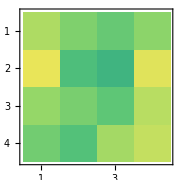

```mathematica
n=1; (*Markov Chain Order*)
F=x//Flatten//DeleteDuplicates//Sort;
G=Map[StringJoin[#]&,Tuples[x//Flatten//DeleteDuplicates//Sort,n]];
TableForm[probM[x,n]//N,TableHeadings->{G,F}]
MatrixPlot[probM[x,n],ImageSize->Small,ColorFunction->"BlueGreenYellow"]
(*You can export the probability transition matrix for further analysis in other programming languages Export["Desktop/TransitionMatrix.csv",probM[x,n]//N,"TableHeadings"->{G,F}]*)
```

| A | C | G | T
AA | 0.302946 | 0.213774 | 0.223726 | 0.259554
AC | 0.394138 | 0.196564 | 0.0783224 | 0.330975
AG | 0.307078 | 0.199772 | 0.237443 | 0.255708
AT | 0.177549 | 0.150268 | 0.347048 | 0.325134
CA | 0.330009 | 0.218495 | 0.200816 | 0.25068
CC | 0.406154 | 0.145641 | 0.0933333 | 0.354872
CG | 0.244718 | 0.234155 | 0.144366 | 0.376761
CT | 0.254222 | 0.162939 | 0.256504 | 0.326335
GA | 0.270238 | 0.218452 | 0.235119 | 0.27619
GC | 0.299372 | 0.163294 | 0.10328 | 0.434054
GG | 0.289277 | 0.243558 | 0.123026 | 0.34414
GT | 0.234099 | 0.158739 | 0.29396 | 0.313201
TA | 0.273907 | 0.284959 | 0.169149 | 0.271985
TC | 0.386993 | 0.135222 | 0.112041 | 0.365744
TG | 0.245871 | 0.246622 | 0.209084 | 0.298423
TT | 0.242179 | 0.197891 | 0.272759 | 0.28717

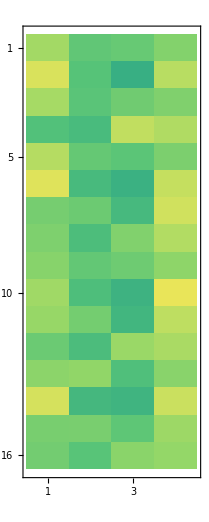

```mathematica
n=2; (*Markov Chain Order*)
F=x//Flatten//DeleteDuplicates//Sort;
G=Map[StringJoin[#]&,Tuples[x//Flatten//DeleteDuplicates//Sort,n]];
TableForm[probM[x,n]//N,TableHeadings->{G,F}]
MatrixPlot[probM[x,n],ImageSize->Small,ColorFunction->"BlueGreenYellow"]
```